# Mathematica for Research

### Student Information Name : Harshad Kumar Elangovan Student ID : 19200349 Course : Data and Computational Science Assignment Number : 06 Due date : "Thu 31 Oct 2019 14:00:00""GMT"

### Basic plotting

Create a single plot of the three functions 4 x^2+5x-2, 2 x^3-4x-1, 7x-3 over the range x∈[-2,2]

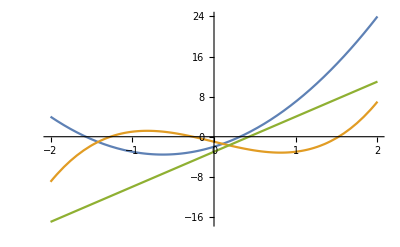

```mathematica
Plot[{4 x^2+ 5 x -2,2 x^3 -4 x -1,7 x -3},{x,-2,2}]
```

Reproduce the plot from the previous question, but make it so that the background is red, there is a Frame which is styled yellow, there are no Axes, it has a PlotLabel of “A few interesting functions” and the curves are White, LightBlue and Green, respectively.

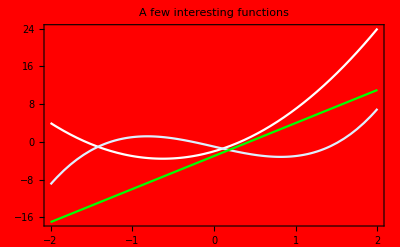

```mathematica
Plot[{4 x^2+ 5 x -2,2 x^3 -4 x -1,7 x -3},{x,-2,2},Background->Red,Frame->True,FrameStyle->Directive[Yellow],Axes-> False,PlotLabel-> "A few interesting functions",PlotStyle->{White,LightBlue,Green}]
```

Reproduce the previous plot, but make it so the first curve is solid, the second is Dashed, and the third is Dotted. Hint: Use Directive to set multiply styles for a curve.

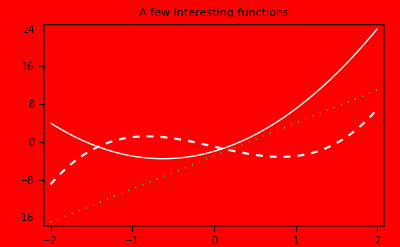

```mathematica
Plot[{4 x^2+ 5 x -2,2 x^3 -4 x -1,7 x -3},{x,-2,2},Background->Red,Frame->True,FrameStyle->Directive[Yellow],Axes-> False,PlotLabel-> "A few interesting functions",PlotStyle->{Directive[White,Thick],Directive[LightBlue,Dashed],Directive[Green,Dotted]}]
```

Use Polygon to show display a hexagon centered on x=2, y=1 with vertices distributed around a circle of radius 3. (Use Show[..., PlotRange→{{-6,6},{-6,6}}] to fix the plot range independently of the parameters of the circle.) Hint: you may find CirclePoints useful.

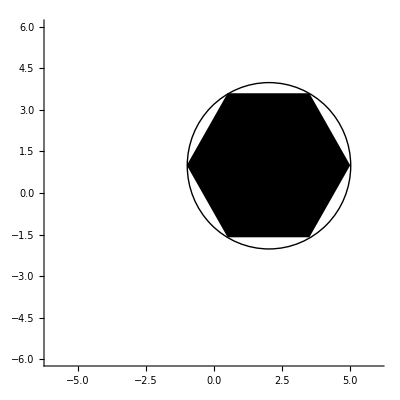

```mathematica
Show[Graphics[Polygon[CirclePoints[{2,1},3,6]]],Graphics[Circle[{2,1},3]],Axes-> True,PlotRange->{{-6,6},{-6,6}}]
```

### Manipulate

Create a Manipulate to plot the function a Sin[x^3]+b Cos[x^2]+c Sin[x]+d, where the parameters a, b, c and d are controlled by the Manipulate.

```mathematica
Manipulate[Plot[a Sin[x^3] + b Cos[x^2] + c Sin[x] + d,{x,-π,π}],{a,0,10},{b,0,10},{c,0,10},{d,0,10}]
```

Create a Manipulate that shows a polygon with sliders to set how many vertices it has, the {x,y} coordinates of the centre, radius and colour (Hue). (Use Show[..., PlotRange→{{-8,8},{-8,8}}] to keep the plot range while the controls are changed.)

```mathematica
Manipulate[Show[Graphics[{Hue[c],Polygon[CirclePoints[{x,y},b,a]]}],Axes->True,PlotRange->{{-8,8},{-8,8}}],{x,0,10},{y,0,10},{a,1,10},{b,0,10},{c,0,100}]
```

A simple harmonic oscillator in one dimension has position x(t)=A_x cos(2 π f_x t+ϕ_x), where t is time, A_x is the amplitude, f_x is the frequency and ϕ_x is an arbitrary phase (the last 3 are constants).  A two dimensional simple harmonic oscillator has position (x(t),y(t)) where y(t)=A_y cos(2 π f_y t+ϕ_y) for other constants A_y,f_y and ϕ_y. Write a manipulate that controls the 6 constants and initial and final times and returns a parametric plot of the position of the two dimensional simple harmonic oscillator.

```mathematica
Manipulate[ParametricPlot[{Ax Cos[2 π fx t + ϕx],Ay Cos[2 π fy t + ϕy]},{t,t1,t2}],{Ax , -10,10},{Ay,-10,10},{fx,0,50},{fy,0,50},{ϕx,-10,10},{ϕy,-10,10},{t1,0,10},{t2,10,50}]
```

### 2D plots

Display a surface plot of the following function: the magnitude (absolute value) of the LogisticSigmoid of z, where z is a complex number; the two axes of the surface plot are x and y and z = x + ⅈ y.

```mathematica
z = x + ⅈ y;
Plot3D[Abs[LogisticSigmoid[z]],{x,-10,10},{y,-10,10},AxesLabel->{x,y,z}]
```

-Graphics3D-

Recreate the previous plot four times but with a different camera ViewPoint each time (choose Top, Left, Front and {3,2,1}).

```mathematica
z = x + ⅈ y;
Plot3D[Abs[LogisticSigmoid[z]],{x,-10,10},{y,-10,10},AxesLabel->{x,y,z},ViewPoint->Top]
```

-Graphics3D-

```mathematica
z = x + ⅈ y;
Plot3D[Abs[LogisticSigmoid[z]],{x,-10,10},{y,-10,10},AxesLabel->{x,y,z},ViewPoint->Left]
```

-Graphics3D-

```mathematica
z = x + ⅈ y;
Plot3D[Abs[LogisticSigmoid[z]],{x,-10,10},{y,-10,10},AxesLabel->{x,y,z},ViewPoint->Front]
```

-Graphics3D-

```mathematica
z = x + ⅈ y;
Plot3D[Abs[LogisticSigmoid[z]],{x,-10,10},{y,-10,10},AxesLabel->{x,y,z},ViewPoint->{3,2,1}]
```

-Graphics3D-

```mathematica
z = x + ⅈ y;
{Plot3D[Abs[LogisticSigmoid[z]],{x,-10,10},{y,-10,10},AxesLabel->{x,y,z},ViewPoint->Top],
Plot3D[Abs[LogisticSigmoid[z]],{x,-10,10},{y,-10,10},AxesLabel->{x,y,z},ViewPoint->Left],
Plot3D[Abs[LogisticSigmoid[z]],{x,-10,10},{y,-10,10},AxesLabel->{x,y,z},ViewPoint->Front],Plot3D[Abs[LogisticSigmoid[z]],{x,-10,10},{y,-10,10},AxesLabel->{x,y,z},ViewPoint->{3,2,1}]}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

Create a contour plot of the real and imaginary parts of the ArcTan function as a function of the complex number z. (Hint: use z=x+ⅈ y and plot as a function of x and y).

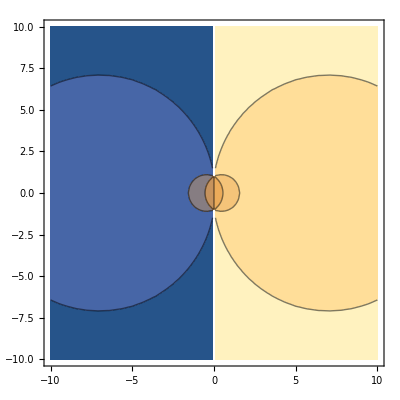

```mathematica
z=x+ⅈ y;
ContourPlot[Re[ArcTan[z]],{x,-10,10},{y,-10,10}]
```

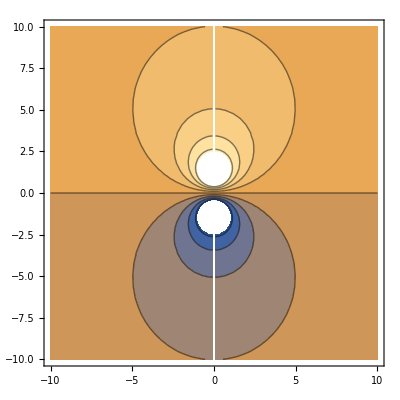

```mathematica
ContourPlot[Im[ArcTan[z]],{x,-10,10},{y,-10,10}]
```